# Biot-Savart magnetic field calculations for wires: Tests

© 2021, Jan. G. Korvink

## Import

```mathematica
Get[NotebookDirectory[]<>"BiotSavart2.m"]
```

## Tutorial

To get started, you need to clarify how this package works:

0. The package is invoked by importing the “BiotSavart2.m” file. This will establish all the needed functionality.

1. Geometrically, all current paths are defined as wire objects. You will construct your coil from one or more of these wire objects. For example, WireSegment[] defines a wire made up of straight segments, whereas WireCircle[] defines a perfect circle wire. You should use the constructor functions to build the wire objects, then the syntax will always be correct: MakeWireSegment[] is such a constructor. 

To facilitate field evaluation speed (see below), efficient closed form solutions were gathered from the literature for special wire shapes. Nevertheless, general shapes are also provided. If you don’t find the shape you need, you can always approximate your coil using the WireSegment[] object, or build the coil shape from a set of WireSpline[] objects, which are defined as cubic Bezier splines.

2. To debug your specification, you should first plot the coil, for which you will use the DrawWire function. It produces 3-dimensional graphical primitives for all the wire elements, which must be wrapped into a Graphics3D header for display. Also remember to check the sense of the wire, indicated by an arrow.

3. Once the coil is specified, you can compute its various field values for a given spatial point. For this you will need one of the following three functions: MagneticVectorPotential[], MagneticInduction[], and MagneticInductionGradient[].

4. You may of course also perform contour plots of the coil fields. 

5. If you get stuck, you should check the help texts. For example, by entering ?Symbol, where Symbol is for example DrawWire, or any other exported symbol of the package

Next we will perform these steps for a few popular coil shapes.

```mathematica
?BiotSavart
```

```mathematica
?WireSpline
```

We first generate a set of spline points on a helix, covering one quarter of a rotation about the z-axis. This is wrapped into a WireSpline, and the process is repeated for rotated and translated versions of the helix.

{{r,0,0},{r,4/3 (-1+√2) r,r/8},{4/3 (-1+√2) r,r,r/8},{0,r,r/4}}

WireGroup[{WireSpline[{{1,0,0},{1,4/3 (-1+√2),1/8},{4/3 (-1+√2),1,1/8},{0,1,1/4}},1,WireColor→RGBColor[1, 0, 0]],WireSpline[{{0,1,1/4},{-4/3 (-1+√2),1,3/8},{-1,4/3 (-1+√2),3/8},{-1,0,1/2}},1,WireColor→RGBColor[1, 0, 0]],WireSpline[{{-1,0,1/2},{-1,-4/3 (-1+√2),5/8},{-4/3 (-1+√2),-1,5/8},{0,-1,3/4}},1,WireColor→RGBColor[1, 0, 0]],WireSpline[{{0,-1,3/4},{4/3 (-1+√2),-1,7/8},{1,-4/3 (-1+√2),7/8},{1,0,1}},1,WireColor→RGBColor[1, 0, 0]]}]

-Graphics3D-

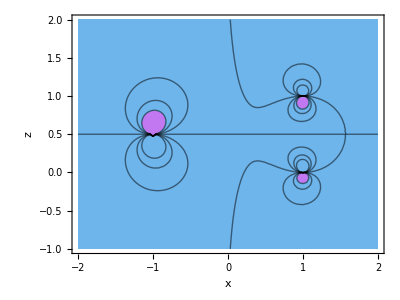

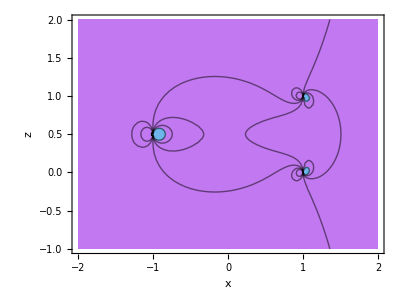

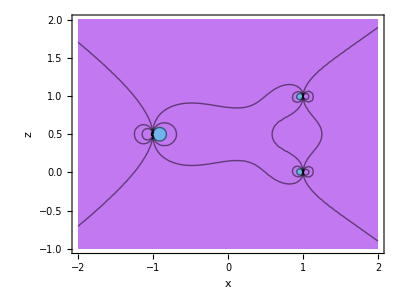

```mathematica
pts={{r,0,0},{r,4r(Sqrt[2]-1)/3,r/8},{4r(Sqrt[2]-1)/3,r,r/8},{0,r,r/4}}
wg=MakeWireGroup[{MakeWireSpline[pts/.r->1,1],MakeWireSpline[((RotationMatrix[π/2,{0,0,1}].#+{0,0,r/4})&/@pts)/.r->1,1],MakeWireSpline[((RotationMatrix[2π/2,{0,0,1}].#+{0,0,2r/4})&/@pts)/.r->1,1],MakeWireSpline[((RotationMatrix[3π/2,{0,0,1}].#+{0,0,3r/4})&/@pts)/.r->1,1]}]
Graphics3D[DrawWire[wg]]
ContourPlot[MagneticInduction[{x,0,z}, wg][[1]],{x,-2,2},{z,-1,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, wg][[2]],{x,-2,2},{z,-1,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, wg][[3]],{x,-2,2},{z,-1,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

## Crossed coil

0.1

WireGroup[{WireSegment[{{-1,-0.1,-1},{1,-0.1,1}},1,WireColor→RGBColor[1, 0, 0]],WireSegment[{{1,0.1,-1},{-1,0.1,1}},1,WireColor→RGBColor[1, 0, 0]]}]

-Graphics3D-

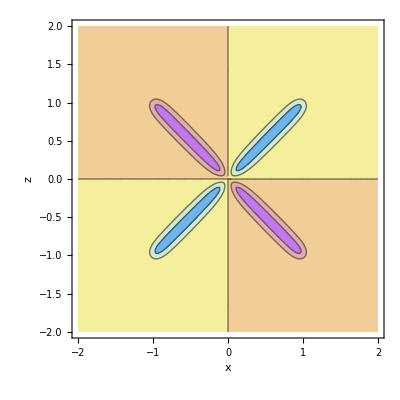

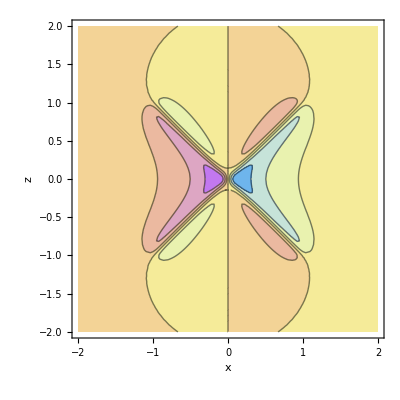

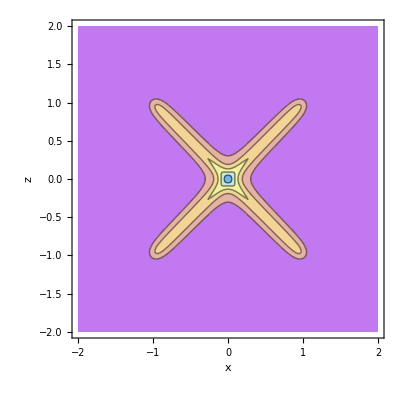

```mathematica
δ=0.1
wg=MakeWireGroup[{MakeWireSegment[{{-1,-δ,-1},{1,-δ,1}},1],MakeWireSegment[{{1,δ,-1},{-1,δ,1}},1]}]
Graphics3D[DrawWire[wg]]
ContourPlot[MagneticInduction[{x,0,z}, wg][[1]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, wg][[2]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, wg][[3]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

## Butterfly coil

```mathematica
Δ={0.5,0,0};
δ=0.1;
w=0.7;
h=1;
z=δ/2;
b=MakeWireGroup[
{MakeWireRectangle[-Δ+{0,0,z},{0,0,1},{w,2h,0},1],
MakeWireRectangle[Δ+{0,0,z},{0,0,1},{w,2h,0},-1],
MakeWireRectangle[-Δ+{0,0,z},{0,0,1},{w+δ,2h+2δ,0},1],
MakeWireRectangle[Δ+{0,0,z},{0,0,1},{w+δ,2h+2δ,0},-1],
MakeWireRectangle[-Δ+{0,0,z},{0,0,1},{w+2δ,2h+4δ,0},1],
MakeWireRectangle[Δ+{0,0,z},{0,0,1},{w+2δ,2h+4δ,0},-1],
MakeWireSegment[{{0,h+2δ,z},{0,-h-2δ,z}},1],
MakeWireSegment[{{0,h+2δ,-z},{0,-h-2δ,-z}},-1],
MakeWireRectangle[-Δ+{0,0,-z},{0,0,1},{w,2h,0},-1],
MakeWireRectangle[Δ+{0,0,-z},{0,0,1},{w,2h,0},1],
MakeWireRectangle[-Δ+{0,0,-z},{0,0,1},{w+δ,2h+2δ,0},-1],
MakeWireRectangle[Δ+{0,0,-z},{0,0,1},{w+δ,2h+2δ,0},1],
MakeWireRectangle[-Δ+{0,0,-z},{0,0,1},{w+2δ,2h+4δ,0},-1],
MakeWireRectangle[Δ+{0,0,-z},{0,0,1},{w+2δ,2h+4δ,0},1]
}];
Graphics3D[DrawWire[b]]
```

-Graphics3D-

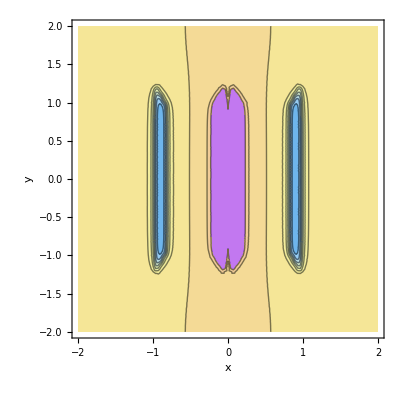

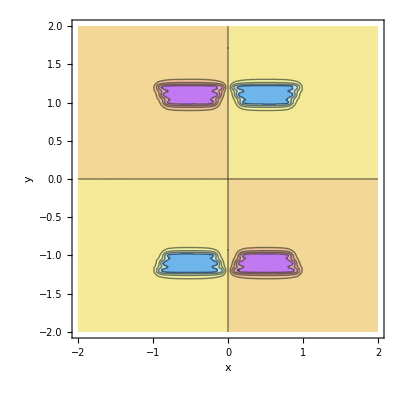

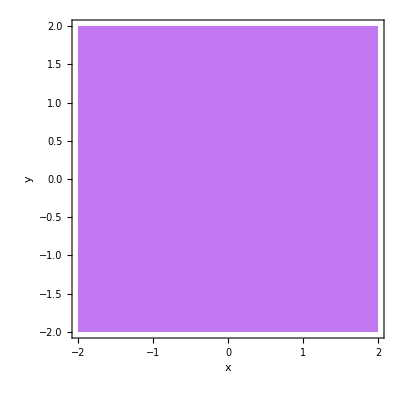

```mathematica
ContourPlot[MagneticInduction[{x,y,0}, b][[1]],{x,-2,2},{y,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,y,0}, b][[2]],{x,-2,2},{y,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,y,0}, b][[3]],{x,-2,2},{y,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

## Helmholtz coil

WireGroup[{WireCircle[{0,0,0.5},{0,0,1},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,0,-0.5},{0,0,1},1,1,WireColor→RGBColor[1, 0, 0]]}]

-Graphics3D-

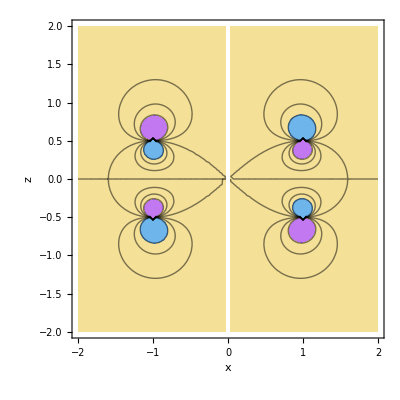

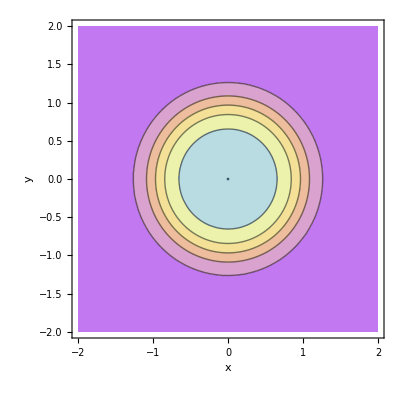

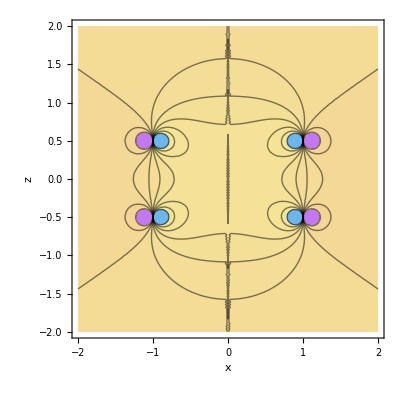

```mathematica
hc=MakeWireGroup[{MakeWireCircle[{0,0,.5},1,1],MakeWireCircle[{0,0,-.5},1,1]}]
Graphics3D[DrawWire[hc]]
ContourPlot[MagneticInduction[{x,0,z}, hc][[1]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,y,0}, hc][[3]],{x,-2,2},{y,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, hc][[3]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

```mathematica
?MakeWireCircle
```

## Anti Helmholtz coil

WireGroup[{WireCircle[{0,0,0.5},{0,0,1},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,0,-0.5},{0,0,1},1,-1,WireColor→RGBColor[1, 0, 0]]}]

-Graphics3D-

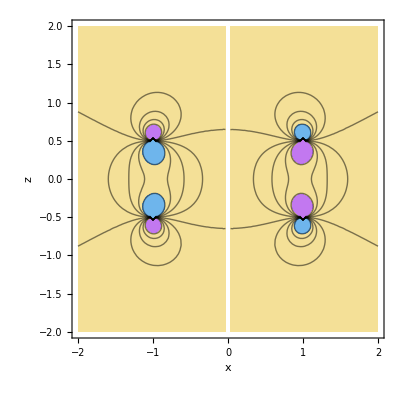

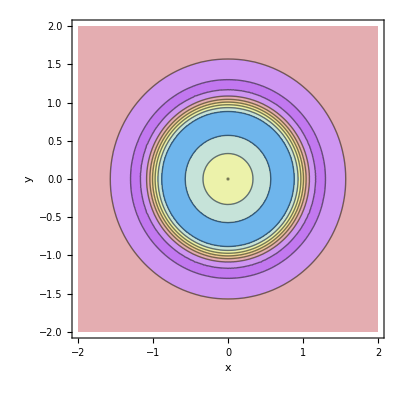

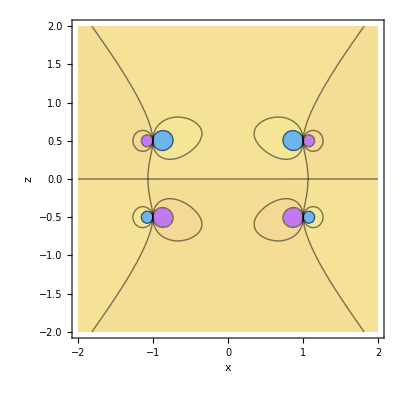

```mathematica
hc=MakeWireGroup[{MakeWireCircle[{0,0,.5},1,1],MakeWireCircle[{0,0,-.5},1,-1]}]
Graphics3D[DrawWire[hc]]
ContourPlot[MagneticInduction[{x,0,z}, hc][[1]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,y,.25}, hc][[3]],{x,-2,2},{y,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{x,0,z}, hc][[3]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

## Toroid coil

8

WireGroup[{WireCircle[{0,2,0},{0,0,1},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,√2,√2},{0,-1/(√2),1/(√2)},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,0,2},{0,-1,0},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,-√2,√2},{0,-1/(√2),-1/(√2)},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,-2,0},{0,0,-1},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,-√2,-√2},{0,1/(√2),-1/(√2)},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,0,-2},{0,1,0},1,1,WireColor→RGBColor[1, 0, 0]],WireCircle[{0,√2,-√2},{0,1/(√2),1/(√2)},1,1,WireColor→RGBColor[1, 0, 0]]}]

RotationMatrix::spln: Vectors {0,0,1} and {0,0,-1} do not define a plane.

General::stop: Further output of RotationMatrix::spln will be suppressed during this calculation.

-Graphics3D-

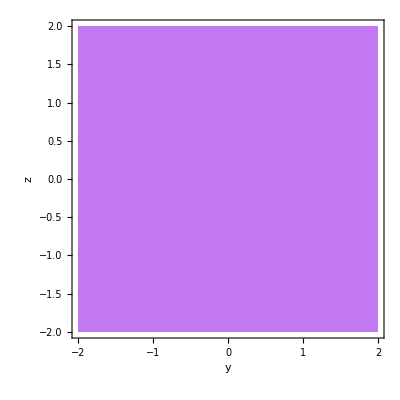

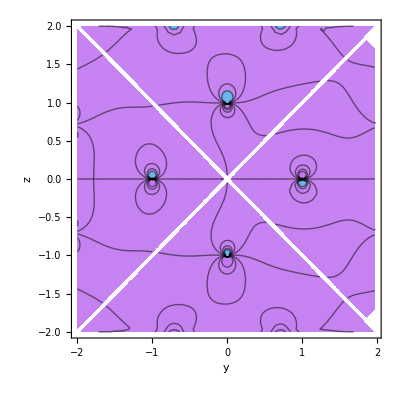

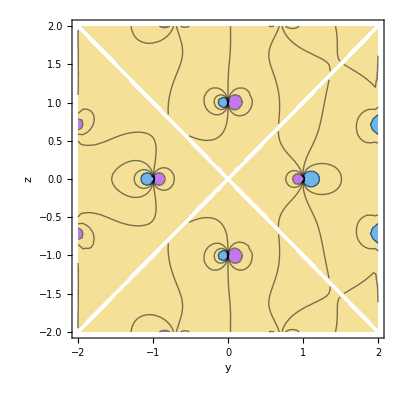

```mathematica
n=8
tc=MakeWireGroup[MakeWireCircle[2{0,Cos[# ],Sin[#]},RotationMatrix[# ,{1,0,0}].{0,0,1},1,1]&/@(Range[0,(n-1)2π/n,2π/n])]
Graphics3D[DrawWire[tc],Axes->True,AxesLabel->Automatic]
ContourPlot[MagneticInduction[{0,y,z}, tc][[1]],{y,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{0,y,z}, tc][[2]],{y,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
ContourPlot[MagneticInduction[{0,y,z}, tc][[3]],{y,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

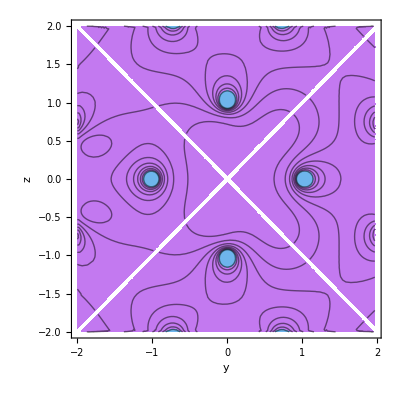

```mathematica
ContourPlot[MagneticInduction[{0,y,z}, tc]//Norm,{y,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

## Circle coil

```mathematica
dw=DrawWire[circ=MakeWireCircle[{0,0,0},1,1]];
dw//Graphics3D
MagneticVectorPotential[{0,0,0},circ]//N
ContourPlot[Evaluate[MagneticVectorPotential[{x,0,z}, circ]][[1]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",AspectRatio->Automatic,PlotPoints->51,PlotRange->{-.0000001,.0000001},Contours->30,FrameLabel->Automatic]
```

-Graphics3D-

{0.,0.,0.}

-Graphics-

```mathematica
ContourPlot[Evaluate[MagneticInduction[{x,0,z}, circ]][[1]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",AspectRatio->Automatic,PlotPoints->51,PlotRange->{-0.0000005,0.0000005},Contours->30,FrameLabel->Automatic]
```

-Graphics-

```mathematica
Plot3D[Evaluate[MagneticInduction[{x,0,z}, circ]][[1]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",PlotPoints->50,PlotRange->{-0.000001,0.000001},AspectRatio->Automatic,Mesh->None]
```

-Graphics3D-

```mathematica
MagneticInductionGradient[{1.01,0,0}, circ]//N
MagneticInductionGradient[{-1.01,0,0}, circ]//N
ContourPlot[Evaluate[MagneticInductionGradient[{x,.1,z}, circ]][[3,1]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",AspectRatio->Automatic,Contours->20,PlotRange->{-10,10},FrameLabel->Automatic]
ContourPlot[Evaluate[MagneticInductionGradient[{x,.1,z}, circ]][[3,3]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",AspectRatio->Automatic,Contours->20,PlotRange->{-10,10},FrameLabel->Automatic]
```

MagneticInductionGradient[{1.01,0.,0.},circ]

MagneticInductionGradient[{-1.01,0.,0.},circ]

Part::partw: Part 3 of MagneticInductionGradient[{-4.99929,0.1,-4.99929},circ] does not exist.

Part::partw: Part 3 of MagneticInductionGradient[{-4.285,0.1,-4.99929},circ] does not exist.

Part::partw: Part 3 of MagneticInductionGradient[{-3.57071,0.1,-4.99929},circ] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Part::partw: Part 3 of MagneticInductionGradient[{-4.99929,0.1,-4.99929},circ] does not exist.

Part::partw: Part 3 of MagneticInductionGradient[{-4.285,0.1,-4.99929},circ] does not exist.

Part::partw: Part 3 of MagneticInductionGradient[{-3.57071,0.1,-4.99929},circ] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Plot3D[Evaluate[MagneticInductionGradient[{x,.1,z}, circ]][[3,3]],{x,-5,5},{z,-5,5},MaxRecursion->4,ColorFunction->"Pastel",AspectRatio->Automatic,PlotRange->{-10,10}]
```

-Graphics3D-

## Arc coil

```mathematica
dw=DrawWire[ac=MakeWireCircularArc[{0,0,.5},1,{0,2π},1]]
dw//Graphics3D
MagneticVectorPotential[{1,1,1},ac]
ContourPlot[Evaluate[MagneticVectorPotential[{x,0,z}, ac]][[2]],{x,-2,2},{z,-2,2},MaxRecursion->4,PlotRange->All,ColorFunction->"Pastel",AspectRatio->Automatic,FrameLabel->Automatic]
```

{RGBColor[1, 0, 0],Arrow[BSplineCurve[{{1.,0.,0.5},{1.,1.,0.5},{0.,1.,0.5},{-1.,1.,0.5},{-1.,0.,0.5},{-1.,-1.,0.5},{0.,-1.,0.5},{1.,-1.,0.5},{1.,0.,0.5}},SplineDegree→2,SplineKnots→{0,0,0,1,1,2,2,3,3,4,4,4},SplineWeights→{1,1/(√2),1,1/(√2),1,1/(√2),1,1/(√2),1}],0.05]}

-Graphics3D-

{0.,0.,0.}

-Graphics-

## Multipole preparation

```mathematica
LegendreP[#,Cos[θ]]&/@Range[0,10]
```

{1,Cos[θ],1/2 (-1+3 Cos[θ]^2),1/2 (-3 Cos[θ]+5 Cos[θ]^3),1/8 (3-30 Cos[θ]^2+35 Cos[θ]^4),1/8 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5),1/16 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6),1/16 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7),1/128 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8),1/128 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9),1/256 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)}

```mathematica
n=40
ListLogPlot[Abs[(0.1^#&/@Range[0,n])*(LegendreP[#,Cos[θ]]&/@Range[0,n])/.{θ->.5π}],Joined->True,PlotRange->All]
N[(0.1^#&/@Range[0,n])*(LegendreP[#,Cos[θ]]&/@Range[0,n])/.{θ->.5π}]
```

40

General::munfl: (6.12323×10^-17)^19 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^20 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^19 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

General::munfl: (6.12323×10^-17)^19 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^20 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^19 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.,6.12323×10^-18,-0.005,-9.18485×10^-20,0.0000375,1.14811×10^-21,-3.125×10^-7,-1.33946×10^-23,2.73438×10^-9,1.50689×10^-25,-2.46094×10^-11,-1.65758×10^-27,2.25586×10^-13,1.79571×10^-29,-2.09473×10^-15,-1.92398×10^-31,1.96381×10^-17,2.04422×10^-33,-1.85471×10^-19,-2.15779×10^-35,1.76197×10^-21,2.26568×10^-37,-1.68188×10^-23,-2.36867×10^-39,1.6118×10^-25,2.46736×10^-41,-1.54981×10^-27,-2.56226×10^-43,1.49446×10^-29,2.65377×10^-45,-1.44464×10^-31,-2.74223×10^-47,1.3995×10^-33,2.82792×10^-49,-1.35834×10^-35,-2.9111×10^-51,1.32061×10^-37,2.99196×10^-53,-1.28585×10^-39,-3.0707×10^-55,1.25371×10^-41}

```mathematica
CosAngle[a:{_,_,_},b:{_,_,_}]:=(a.b)/(Sqrt[a.a]Sqrt[b.b]);

BuildMultipole[p:{_,_,_},WireSegment[s:{p1:{_,_,_},p2:{_,_,_}},current_,spec:OptionsPattern[]]]:=
Block[{l2,lp,mc,n,σ},
If[p-mc=={0,0},Return[0]];
l=√((p2-p1).(p2-p1));
lp=√(p.p);
If[lp<2l,Return[0]];
n=5;
x[sss_]:=p1+sss(p2-p1)-mc;
If[lp==0,Return[Indeterminate]];
mc=(p1+p2)/2;
Plus@@((lp^(-(#+1)) NIntegrate[If[Abs[Chop[x[σ]]]=={0,0,0},1,(√(x[σ].x[σ]))^# LegendreP[#,CosAngle[p-mc,x[σ]]]],{σ,0,1,.1},MaxRecursion->0,Method->{"LobattoKronrodRule","SymbolicProcessing"->False}])&/@Range[0,n])
];
Timing[BuildMultipole[{0,0,2},MakeWireSegment[{{-.1,0,0},{.1,0,0}},J]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.8388}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.2388}. NIntegrate obtained -0.00040668 and 0.000093836 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.7592}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.185162,0.0499492}

```mathematica
Plot[BuildMultipole[{0,0,z},MakeWireSegment[{{-.1,0,0},{.1,0,0}},J]],{z,10,100},PlotRange->All]//Timing
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.8388}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.2388}. NIntegrate obtained -0.00040668 and 0.000093836 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.8388}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{18.722,-Graphics-}

```mathematica
?WireSegment
```

```mathematica
MakeWireSegment[{{-1,0,0},{1,0,0}}]
```

MakeWireSegment[{{-1,0,0},{1,0,0}}]

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.7592}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.3582}. NIntegrate obtained -0.00040668 and 0.000101577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in σ near {σ} = {0.7592}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.17046,0.0499492}

```mathematica
Theta[s_]:=s 2 π/;(s≥0&&s≤1);
Rdash[ϕ_]:={Sin[ϕ],0,Cos[ϕ]}/;(ϕ≥0&&ϕ≤π/2);
Rel[s_]:={Cos[Theta[s]],Sin[Theta[s]],0};
CosAlpha[u:{_,_,_},v:{_,_,_}]:=(u.v);
ContourPlot[CosAlpha[Rel[s],Rdash[ϕ]],{ϕ,0,π/2},{s,0,1}]
f=FunctionInterpolation[CosAlpha[Rel[s],Rdash[ϕ]],{ϕ,0,π/2},{s,0,1}]
```

```mathematica
ContourPlot[f[ϕ,s],{ϕ,0,π/2},{s,0,1}]
```

-Graphics-

```mathematica
g=FunctionInterpolation[NIntegrate[LegendreP[4,f[ϕ,s]],{s,0,1}],{ϕ,0,π/2}]
Plot[g[ϕ],{ϕ,0,π/2}]
```

NIntegrate::inumr: The integrand 1/8 (3-30 (InterpolatingFunction[{{0,Times[«2»]},{0,1}},«3»,{Automatic,Automatic}][ϕ,s])^2+35 (InterpolatingFunction[{{0,Times[«2»]},{0,1}},{5,3,0,{11,11},{4,4},0,0,0,0,Automatic,{},{},False},{«1»},{{{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»},{«1»}},«9»,{{«1»},{«1»},{«1»},{«1»},«3»,{«1»},{«1»},{«1»},{«1»}}},{Automatic,Automatic}][«1»])^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction[…]

-Graphics-

```mathematica
Plot[Theta[s],{s,0,1}]
Plot[Cos[Theta[s]],{s,0,1}]
Plot[Sin[Theta[s]],{s,0,1}]
```

-Graphics-

-Graphics-

-Graphics-

## Multipoles

```mathematica
Quit[]
```

```mathematica
w=MakeWireSegment[{{0,0,-.5},{0,0,.5}},1]
DrawWire[w]//Graphics3D
m=MakeMultipoleSegment[MakeWireSegment[{{0,0,-.5},{0,0,.5}},1],"VectorPotential"]
```

```mathematica
PlotLimits=5;
ContourPlot[MagneticVectorPotential[{x,0,z},m],{x,-PlotLimits,PlotLimits},{z,-PlotLimits,PlotLimits},Contours->20,PlotRange->{-10^-6,10^-6},Axes->True,AxesLabel->Automatic]
ContourPlot[MagneticVectorPotential[{0,y,z},m],{y,-PlotLimits,PlotLimits},{z,-PlotLimits,PlotLimits},Contours->20,PlotRange->{-10^-6,10^-6},Axes->True,AxesLabel->Automatic]

ContourPlot[MagneticVectorPotential[{x,0,z},w][[1]],{x,-PlotLimits,PlotLimits},{z,-PlotLimits,PlotLimits},Contours->20,PlotRange->{-10^-6,10^-6},Axes->True,AxesLabel->Automatic]
ContourPlot[MagneticVectorPotential[{0,y,z},w],{y,-PlotLimits,PlotLimits},{z,-PlotLimits,PlotLimits},Contours->20,PlotRange->{-10^-6,10^-6},Axes->True,AxesLabel->Automatic]
```

RotationMatrix::spln: Vectors {0,0,-1.} and {0,0,1} do not define a plane.

-Graphics-

RotationMatrix::spln: Vectors {0,0,-1.} and {0,0,1} do not define a plane.

-Graphics-

RotationMatrix::spln: Vectors {0,0,-1.} and {0,0,1} do not define a plane.

-Graphics-

RotationMatrix::spln: Vectors {0,0,-1.} and {0,0,1} do not define a plane.

-Graphics-

```mathematica
l=m[[1,4]]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Plot[l[[1]][0]/r,{r,.5,10}]
Plot[l[[2]][0]/r^2,{r,.5,10}]
Plot[l[[3]][0]/r^3,{r,.5,10}]
Plot[l[[4]][0]/r^4,{r,.5,10}]
```

```mathematica
ContourPlot[l[[1]][θ]/r+l[[2]][θ]/r^2+l[[3]][θ]/r^3+l[[4]][θ]/r^4,{r,.5,10},{θ,0,2π},Axes->True,AxesLabel->Automatic,AspectRatio->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
PolarPlot[(l[[1]][θ]/r+l[[2]][θ]/r^2+l[[3]][θ]/r^3+l[[4]][θ]/r^4)/.r->.35,{θ,0,2π},Axes->True,AxesLabel->Automatic,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Partition[{{-0.5,-0.5,0},{0.5,-0.5,0},{0.5,0.5,0},{-0.5,0.5,0},{-0.5,-0.5,0}},2,1]
```

{{{-0.5,-0.5,0},{0.5,-0.5,0}},{{0.5,-0.5,0},{0.5,0.5,0}},{{0.5,0.5,0},{-0.5,0.5,0}},{{-0.5,0.5,0},{-0.5,-0.5,0}}}

```mathematica
Plot[Sign[s-0.5],{s,0,1}]
```

-Graphics-

```mathematica
m
```

MultipoleSegment[VectorPotentialMultipole[{0,0,0.},1.,5.,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}],WireSegment[{{0,0,-0.5},{0,0,0.5}},1,WireColor→RGBColor[1, 0, 0]]]

```mathematica
BuildVectorPotentialMultipoleFunction[vpm:VectorPotentialMultipole[cg:{_,_,_},r1_,r2_,mpfs:{(_)..}],r_,i_Integer]:=r^-i mpfs[[i]][ϕ];
```

```mathematica
BuildVectorPotentialMultipoleFunction[m[[1]],r,1]
```

(InterpolatingFunction[…][ϕ])/r

```mathematica
PolarPlot[BuildVectorPotentialMultipoleFunction[m[[1]],r,#]/.r->10,{ϕ,0,2π},Axes->True,AxesLabel->Automatic,AspectRatio->Automatic,PlotRange->All]&/@Range[1,10,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PolarPlot[LegendreP[#,Cos[ϕ]],{ϕ,0,2π},Axes->True,AxesLabel->Automatic,AspectRatio->Automatic,PlotRange->All]&/@Range[0,10,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Square multipole

```mathematica
w=MakeWireSegment[{{-0.5,-0.5,0},{0.5,-0.5,0},{0.5,0.5,0},{-0.5,0.5,0},{-0.5,-0.5,0}},1]
DrawWire[w]//Graphics3D
MakeMultipoleSegment[w,"VectorPotential"]
```

WireSegment[{{-0.5,-0.5,0},{0.5,-0.5,0},{0.5,0.5,0},{-0.5,0.5,0},{-0.5,-0.5,0}},1,WireColor→RGBColor[1, 0, 0]]

-Graphics3D-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in Private`s near {Private`s} = {1.}. NIntegrate obtained 0.102473 and 0.0412055 for the integral and error estimates.

NIntegrate::inumr: The integrand √((InterpolatingFunction[{{1,5}},{5,3,0,{5},{2},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5}},{{0},{0},{0},{0},{0}},{Automatic}][1+4 Private`s])^2+(0.1+InterpolatingFunction[«1»][«1»])^2+(0.1+InterpolatingFunction[{{«2»}},«3»,{Automatic}][1+Times[«2»]])^2) InterpolatingFunction[«1»][Private`ϕ,Private`s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in Private`s near {Private`s} = {1.}. NIntegrate obtained 4.09519×10^-19 and 4.09519×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in Private`s near {Private`s} = {1.}. NIntegrate obtained 0.0133756 and 0.00537848 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

MultipoleSegment[VectorPotentialMultipole[{-0.1,-0.1,0},1,1,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}],WireSegment[{{-0.5,-0.5,0},{0.5,-0.5,0},{0.5,0.5,0},{-0.5,0.5,0},{-0.5,-0.5,0}},1,WireColor→RGBColor[1, 0, 0]]]

```mathematica
l=%[[1,4]]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Plot[Chop[l[[8]]][x],{x,0,1.57}]
```

-Graphics-

```mathematica
Interpolation[#,InterpolationOrder->1]&/@Transpose[{{-0.5,0,0},{0,0,0},{0.5,0,0}}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
{x,y,z}=Interpolation[#,InterpolationOrder->1]&/@Transpose[{{-0.5,0,0},{0,0,0},{0.5,0,0}}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
R[s_]:=Block[{t},t=(3-1)s+1;{x[t],y[t],z[t]}-{0,0,0}];
```

```mathematica
R[1]
```

{0.5,0,0}

```mathematica
f=ListInterpolation[{{-0.5,0,0},{0,0,0},{0.5,0,0}},InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
f[1.1,2.2]
```

0.

```mathematica
Plot[%[s],{s,0,1}]
```

-Graphics-

```mathematica
Transpose[{{-0.5,0,0},{0,0,0},{0.5,0,0}}]
```

{{-0.5,0,0.5},{0,0,0},{0,0,0}}